```mathematica
SetDirectory[NotebookDirectory[]];
<<rotationtools.wl
```

```mathematica
(*Writing modules to create pure translation and pure rotation quaternions*)
```

```mathematica
(*Quaternion Modules*)
```

```mathematica
quat[θ_,k_ ]:=Module[{},
Return[{Cos[θ/2], Sin[θ/2]{k[[1]], k[[2]], k[[3]]}}];
]
```

```mathematica
qmult[q1_, q2_]:=Module[{},
Return[{q1[[1]]*q2[[1]]-q1[[2]].q2[[2]], q1[[1]]*q2[[2]]+q1[[2]]*q2[[1]]+Cross[q1[[2]], q2[[2]]]}];
]
```

```mathematica
cquat[q_]:=Module[{},
Return[{q[[1]], -q[[2]]}];
];
```

```mathematica
(*Dual Quaternion Modules*)
```

```mathematica
(*Module for unit dual quaternions, given a unit rotation θ, axis, k and translation t. This module is to produce a dual quaternion representing a translation followed by rotation*)
```

```mathematica
unitdq[ t_, θ_, k_]:=Module[{qrot},
qrot = quat[θ, k];
Return[{qrot, qmult[{0,t}, qrot]/2}];
]
```

```mathematica
cdualq[dq1_]:=Module[{},
Return[{cquat[dq1[[1]]], cquat[dq1[[2]]]}];
];
```

```mathematica
dqmult[dq1_, dq2_]:=Module[{},
Return[ {qmult[dq1[[1]], dq2[[1]]], qmult[dq1[[2]], dq2[[1]]]+qmult[dq1[[1]], dq2[[2]]]}];
]
```

```mathematica
qt = quat[0, {2, 0, 0}];
q1 = quat[ π/3, {1, 0, 0}];
q2 = quat[π/6, {1, 0, 1}];
```

```mathematica
N[q2]
N[cquat[q2]]
```

{0.965926,{0.258819,0.,0.258819}}

{0.965926,{-0.258819,0.,-0.258819}}

```mathematica
qmult[q1, q2]
```

{-(-1+√3)/(4 √2)+1/4 √(3/2) (1+√3),{1/4 √(3/2) (-1+√3)+(1+√3)/(4 √2),-(√(3/2))/4+1/(4 √2),1/4 √(3/2) (-1+√3)}}

```mathematica
dq1 = unitdq[{1,1,1}, π/3, {0,0,1}]
dq2 = unitdq[{1,0,1}, π/6, {1,0,1}]
```

{{(√3)/2,{0,0,1/2}},{-1/4,{1/2 (1/2+(√3)/2),1/2 (-1/2+(√3)/2),(√3)/4}}}

{{(1+√3)/(2 √2),{(-1+√3)/(2 √2),0,(-1+√3)/(2 √2)}},{-(-1+√3)/(2 √2),{(1+√3)/(4 √2),0,(1+√3)/(4 √2)}}}

```mathematica
N[dqmult[dq1, dq2]]
```

{{0.707107,{0.224144,0.12941,0.707107}},{-0.995955,{1.06066,0.353553,0.595035}}}

```mathematica
N[dq1]
N[cdualq[dq1]]
```

{{0.866025,{0.,0.,0.5}},{-0.25,{0.683013,0.183013,0.433013}}}

{{0.866025,{0.,0.,-0.5}},{-0.25,{-0.683013,-0.183013,-0.433013}}}

```mathematica
(*Testing the Hamiltonian Operator of a given quaternion*)
```

```mathematica
Hp[q_] := Module[{a0, a1, a2, a3},
a0 = q[[1]];a1 = q[[2]][[1]];a2 = q[[2]][[2]];a3 = q[[2]][[3]];
Return[{{a0, -a1, -a2, -a3},{a1, a0, -a3, a2},{a2, a3, a0, -a1},{a3, -a2, a1, a0}}];
]
```

```mathematica
Hn[q_] := Module[{a0, a1, a2, a3},
a0 = q[[1]];a1 = q[[2]][[1]];a2 = q[[2]][[2]];a3 = q[[2]][[3]];
Return[{{a0, -a1, -a2, -a3},{a1, a0, a3, -a2},{a2, -a3, a0, a1},{a3, a2, -a1, a0}}];
]
```

```mathematica
dHp[dq1_]:=Module[{},
Return[N[ArrayFlatten[{{Hp[dq1[[1]]], ConstantArray[0,{4,4}]},{Hp[dq1[[2]]], Hp[dq1[[1]]]}}]]];
]
```

```mathematica
dHn[dq1_]:=Module[{},
Return[N[ArrayFlatten[{{Hn[dq2[[1]]], ConstantArray[0,{4,4}]},{Hn[dq2[[2]]], Hn[dq2[[1]]]}}]]];
]
```

```mathematica
(*Verification of the properties of the Hamiltonian Operator*)
```

```mathematica
Flatten[N[qmult[q1,q2]]]
N[Hp[q1].Flatten[q2]]
N[Hn[q2].Flatten[q1]]
```

{0.707107,0.707107,-0.12941,0.224144}

{0.707107,0.707107,-0.12941,0.224144}

{0.707107,0.707107,-0.12941,0.224144}

```mathematica
Flatten[N[dqmult[dq1, dq2]]]
dHp[dq1].Flatten[dq2]
dHn[dq2].Flatten[dq1]
```

{0.707107,0.224144,0.12941,0.707107,-0.995955,1.06066,0.353553,0.595035}

{0.707107,0.224144,0.12941,0.707107,-0.995955,1.06066,0.353553,0.595035}

{0.707107,0.224144,0.12941,0.707107,-0.995955,1.06066,0.353553,0.595035}

```mathematica
(*Now define the FK of the interms of the six angles at each of the joint*)
```

```mathematica
(*Using the DH parameters of PUMA 560 robot*)
```

```mathematica
(*Rotation about the first axis, θ1*)
```

```mathematica
pq1 = unitdq[{0,0,0},θ1, {0,0,1}];
pq2 = unitdq[{0,0,0},-π/2, {1,0,0}];
pq3 = unitdq[{0,0,0},θ2, {0,0,1}];
pq4 =unitdq[{a2,0,0},0,{1,0,0}];
pq5 =unitdq[{0,0,d3},θ3,{0,0,1}];
pq6 = unitdq[{0, 0, 0}, -π/2, {1, 0, 0}];
pq7 = unitdq[{a3,0,0},0,{1,0,0}];
pq8 = unitdq[{0,0,d4},θ4,{0,0,1}];
pq9 = unitdq[{0,0,0},π/2,{1,0,0}];
pq10 = unitdq[{0,0,0},θ5,{0,0,1}];
pq11 = unitdq[{0,0,0},-π/2,{1,0,0}];
pq12 = unitdq[{0,0,0},θ6,{0,0,1}];
```

```mathematica
(*Now computing the fk quaternion*)
```

```mathematica
fkq = Simplify[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[pq1, pq2], pq3], pq4], pq5], pq6], pq7], pq8], pq9], pq10], pq11], pq12]];
```

```mathematica
(*Validation of the FK*)
```

```mathematica
params = {a2->0.4318 , d3->0.125, a3->0.019, d4->0.432};
sampleangles = {θ1->π/4, θ2->π/3, θ3->3π/4, θ4->π/6, θ5->-π/4, θ6->2π/3};
sampleangles2 = {θ1->π/2, θ2->π/6, θ3->π/3, θ4->3π/4, θ5->-π/3, θ6->2π/3};
```

```mathematica
fkqs = N[fkq/.params/.sampleangles]
```

{{-0.954287,{-0.277118,0.0495229,-0.100444}},{0.0128805,{-0.0788202,-0.146687,0.0227634}}}

```mathematica
fkqs2 = N[fkq/.params/.sampleangles2]
```

{{0.135299,{-0.29516,0.326641,-0.887626}},{-0.113218,{0.0556712,-0.0247371,-0.044873}}}

```mathematica
(*Finding the homogeneous transformation matrix from the dual quaternion*)
```

```mathematica
halfsin = Norm[fkqs[[1]][[2]]];
θs = 2*ArcTan[fkqs[[1]][[1]], Norm[fkqs[[1]][[2]]]];
kvecs = fkqs[[1]][[2]]/halfsin;
```

```mathematica
halfsin2 = Norm[fkqs2[[1]][[2]]];
θs2 = 2*ArcTan[fkqs2[[1]][[1]], Norm[fkqs2[[1]][[2]]]];
kvecs2 = fkqs2[[1]][[2]]/halfsin2;
```

```mathematica
Amats = vec2SkewMat[Tan[θs/2]*kvecs];
Amats2 = vec2SkewMat[Tan[θs2/2]*kvecs2];
```

```mathematica
(*Verifications*)
```

```mathematica
Rmats = Inverse[IdentityMatrix[3]-Amats].(IdentityMatrix[3]+Amats)//MatrixForm
```

(0.974917 | -0.219152 | -0.0388486
0.164257 | 0.826234 | -0.538849
0.150188 | 0.518952 | 0.841506)

```mathematica
Rmats2 = Inverse[IdentityMatrix[3]-Amats2].(IdentityMatrix[3]+Amats2)//MatrixForm
```

(-0.789149 | 0.0473672 | 0.612372
-0.433013 | -0.75 | -0.5
0.435596 | -0.65974 | 0.612372)

```mathematica
tempt = {0, {tx, ty, tz}};
```

```mathematica
temptsol = Solve[((qmult[tempt, fkqs[[1]]] - 2*fkqs[[2]])[[2]])==0 ,{tx, ty, tz}][[1]]
```

{tx→0.13036,ty→0.307137,tz→0.0482477}

```mathematica
temptsol2 = Solve[((qmult[tempt, fkqs2[[1]]] - 2*fkqs2[[2]])[[2]])==0 ,{tx, ty, tz}][[1]]
```

{tx→-0.125,ty→-0.0580502,tz→-0.2349}

```mathematica
(*Residues*)
```

```mathematica
(qmult[tempt, fkqs[[1]]]-2*fkqs[[2]])/.temptsol
```

{5.89806×10^-17,{-6.93889×10^-18,5.55112×10^-17,1.38778×10^-17}}

```mathematica
(qmult[tempt, fkqs2[[1]]]-2*fkqs2[[2]])/.temptsol2
```

{-2.498×10^-16,{0.,1.38778×10^-17,6.93889×10^-18}}

```mathematica
(*Now we have an FK quaternion. We have to formulate the Jacobian in q terms. For which we flatten the quaternion and take the derivative wrt all the angles*)
```

```mathematica
flatfkq = Flatten[fkq];
```

```mathematica
(*Now computing the Jacobian, wrt θ*)
```

```mathematica
θsym = {θ1, θ2, θ3, θ4, θ5, θ6};
```

```mathematica
Jquatθ = D[flatfkq, {θsym}];
```

```mathematica
Jquatθs = N[Jquatθ/.params/.sampleangles];
```

```mathematica
(* Now we can proceed to do a kinematic control, assuming (wrongly) that the error is qe = qd-qc *)
```

```mathematica
(*Since the computation of pseudo inverse is tricky and expensive we keep it aside and go with J^T*)
```

```mathematica
(*Using Transpose[Jquatθ]*)
```

```mathematica
qetemp = MatrixExp[Jquatθs.Transpose[Jquatθs]].ConstantArray[0.1,{8,1}]
```

{{0.0926826},{0.0969273},{0.137584},{0.196529},{0.094762},{0.107543},{0.102368},{0.0985833}}

```mathematica
Transpose[Jquatθs].qetemp
```

{{-0.107172},{-0.00513511},{-0.0373443},{-0.116087},{-0.0158783},{-0.0719511}}

```mathematica
(*Then do an Euler step to find the θ at the current instant*)
```

```mathematica
(*Desired quaternion is*)
```

```mathematica
qd = N[fkq/.params/.sampleangles2]
```

{{0.135299,{-0.29516,0.326641,-0.887626}},{-0.113218,{0.0556712,-0.0247371,-0.044873}}}

```mathematica
(*Initial quaternion is*)
```

```mathematica
qi = N[fkq/.params/.sampleangles]
```

{{-0.954287,{-0.277118,0.0495229,-0.100444}},{0.0128805,{-0.0788202,-0.146687,0.0227634}}}

```mathematica
(*Initial error (wrongly) *)
```

```mathematica
qei = qd-qi
```

{{1.08959,{-0.0180424,0.277118,-0.787183}},{-0.126099,{0.134491,0.12195,-0.0676363}}}

```mathematica
(*Error dynamics is*)
```

```mathematica
KMat[θval_]:=Module[{k},
k = 100;
Return[N[Jquatθ.Transpose[Jquatθ].(k*IdentityMatrix[8])/.params/.Inner[Rule, θsym, θsym/.sampleangles,List]]];
]
```

```mathematica
K2Mat[θval_]:=Module[{k},
k = 100;
Return[N[Transpose[Jquatθ].(k*IdentityMatrix[8])/.params/.Inner[Rule, θsym, θsym/.sampleangles,List]]];
]
```

```mathematica
Jqtp = Jquatθ/.params;
```

```mathematica
cJqtp = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real}, {θ5, _Real},{θ6, _Real}}, Evaluate[Jqtp]];
```

```mathematica
cJqtps=cJqtp[(θsym/.sampleangles)[[1]], (θsym/.sampleangles)[[2]], (θsym/.sampleangles)[[3]], (θsym/.sampleangles)[[4]], (θsym/.sampleangles)[[5]], (θsym/.sampleangles)[[6]]]
```

{{0.0502218,-0.115485,-0.115485,0.069337,-0.132376,0.0502218},{-0.0247614,0.301879,0.301879,-0.120432,0.438329,0.0247614},{-0.138559,-0.372904,-0.372904,-0.21197,-0.195078,0.138559},{-0.477144,0.080467,0.080467,-0.430996,-0.0478354,-0.477144},{-0.0113817,0.0239944,0.0649279,0.050799,0.0025415,-0.0113817},{0.0733433,0.00349412,-0.141299,-0.0565544,-0.0112683,-0.0733433},{-0.0394101,0.012602,-0.130201,0.035835,-0.0066367,0.0394101},{0.00644026,0.0797287,0.019899,0.00635106,-0.0832222,0.00644026}}

```mathematica
Bmat[z_/;VectorQ[z, NumericQ]] := Module[{k, Bmattemp, Jqtpval, b2temp},
k = 850;
Jqtpval = cJqtp[z[[1]], z[[2]], z[[3]], z[[4]], z[[5]], z[[6]]];
Bmattemp = N[ArrayFlatten[{{ConstantArray[0,{14,6}],ArrayFlatten[{{Transpose[Jqtpval]*k}, {-Jqtpval.Transpose[Jqtpval]*k}}]}}]];
b2temp = Bmattemp.z;
Return[b2temp];
]
```

```mathematica
motionsim = NDSolve[{Bmat[z[t]]== z'[t],z[0]==Join[θsym/.sampleangles,Flatten[qei]]},z,{t, 0, 15}][[1]];
```

```mathematica
(*Final value reached vs desired value*)
```

```mathematica
thf = Flatten[z[t]/.motionsim/.t->15][[1;;6]]
thd = N[Flatten[θsym/.sampleangles2]]
```

{1.56528,0.526711,1.04681,2.35281,-1.04918,2.10112}

{1.5708,0.523599,1.0472,2.35619,-1.0472,2.0944}

```mathematica
(*Error in the quaternions*)
```

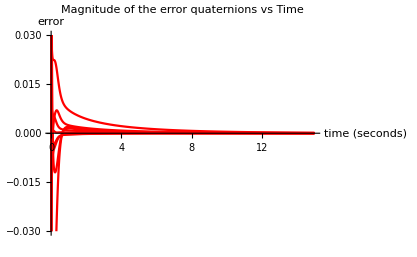

```mathematica
Plot[(z[t]/.motionsim)[[7;;14]], {t, 0, 15}, PlotStyle->Red, PlotRange->{{0,15},{-0.03,0.03}},AxesLabel->{"time (seconds) ", "error"}, PlotLabel->"Magnitude of the error quaternions vs Time"]
```

```mathematica
(*Angles converging*)
```

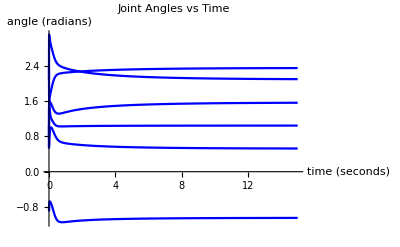

```mathematica
Plot[(z[t]/.motionsim)[[1;;6]], {t, 0, 15}, PlotStyle->Blue, AxesLabel-> {"time (seconds)", "angle (radians)"}, PlotLabel->"Joint Angles vs Time"]
```

```mathematica
(* Bringing the errors to within 2% *)
```

```mathematica
(Abs[thf-thd]/thd)*100
```

{0.351207,0.594389,0.0372528,0.143809,-0.189623,0.320912}

```mathematica
(*Peak overshoot among all the other peaks*)
```

```mathematica
Table[Max[Abs[Table[((z[t]/.motionsim/.t->tval)[[1]][[j]])-thd[[j]],{tval, 0,10, 0.01 }]]], {j, 1, 6}]
```

Part::partd: Part specification 0.785398⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.54456⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1.55708⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{Max[Abs[-1.5708+0.785398⟦1⟧],Abs[-1.5708+1.31799⟦1⟧],Abs[-1.5708+1.31802⟦1⟧],Abs[-1.5708+1.31804⟦1⟧],Abs[-1.5708+1.31814⟦1⟧],Abs[-1.5708+1.3182⟦1⟧],989,Abs[-1.5708+1.56963⟦1⟧],Abs[-1.5708+1.5748⟦1⟧],Abs[-1.5708+1.5765⟦1⟧],Abs[-1.5708+1.57857⟦1⟧],Abs[-1.5708+1.58007⟦1⟧],Abs[-1.5708+1.58052⟦1⟧]],Max[1],2,Max[1],Max[1]}
 |  |  |  |

```mathematica
(*Max steady state error*)
```

```mathematica
Max[Abs[thf-thd]]
```

0.00672117

```mathematica
(*Tuning the value of k for settling time and peak overshoot*)
```

```mathematica
(*This integration gives the angles at each instant of time and also the plot of error asymptotically decreasing with time*)
```

```mathematica
(*Error measure needs to be changed and explanation on why this worked in this paper needs to be given*)
```

```mathematica
(*Cooperative task-space control with two PUMA 560's*)
```

```mathematica
(*Primitive-1: Relative dual position control, so the controlled variable is qr. So we need the Jacbian for this control*)
```

```mathematica
(*We need fk of two robots in the cooperative workspace*)
```

```mathematica
αsym = {θ1, θ2, θ3, θ4, θ5, θ6}/.{θ1->α1, θ2->α2, θ3->α3, θ4->α4, θ5->α5, θ6->α6};
βsym = {θ1, θ2, θ3, θ4, θ5, θ6}/.{θ1->β1, θ2->β2, θ3->β3, θ4->β4, θ5->β5, θ6->β6};
```

```mathematica
fkq1 = fkq/.{θ1->α1, θ2->α2, θ3->α3, θ4->α4, θ5->α5, θ6->α6}/.params;
fkq2 = fkq/.{θ1->β1, θ2->β2, θ3->β3, θ4->β4, θ5->β5, θ6->β6}/.params;
```

```mathematica
Jq1 = D[Flatten[fkq1], {αsym}];
```

```mathematica
cq2 = cdualq[fkq2];
```

```mathematica
Jcq2 = D[Flatten[cq2], {βsym}];
```

```mathematica
sampleα = sampleangles/.{θ1->α1, θ2->α2, θ3->α3, θ4->α4, θ5->α5, θ6->α6};
sampleβ = sampleangles2/.{θ1->β1, θ2->β2, θ3->β3, θ4->β4, θ5->β5, θ6->β6};
```

```mathematica
Jqr = ArrayFlatten[{{dHn[fkq1].Jcq2, dHp[cq2].Jq1}}];
```

```mathematica
Jqr/.sampleα/.sampleβ//MatrixForm
```

(0.403929 | -0.202331 | -0.202331 | 0.234426 | -0.142551 | 0.48847 | 0.39237 | -0.297958 | -0.297958 | 0.358253 | -0.168548 | 0.468271
0.310819 | 0.142015 | 0.142015 | -0.368911 | -0.320202 | -0.0810846 | 0.290316 | 0.311473 | 0.311473 | 0.333102 | 0.209015 | 0.0510397
0.0827721 | 0.453452 | 0.453452 | 0.218408 | -0.379168 | -0.11779 | 0.0837036 | 0.231474 | 0.231474 | -0.0310136 | 0.420037 | 0.165155
0.0113263 | 0.00469152 | 0.00469152 | 0.167313 | -0.0113263 | 0.0877194 | -0.068964 | -0.103081 | -0.103081 | -0.0986711 | -0.0383759 | 0.0290064
-0.150851 | -0.0286134 | 0.0718232 | 0.104827 | 0.211445 | 0.000501816 | -0.0240036 | -0.0289431 | 0.0257937 | 0.0396622 | 0.121734 | 0.0409403
0.230006 | 0.0838916 | 0.27977 | 0.259104 | -0.308914 | 0.210298 | 0.0338636 | -0.0386989 | 0.100091 | -0.0179154 | -0.00238674 | -0.0739879
-0.158781 | -0.0355395 | -0.0517413 | 0.328897 | 0.177772 | 0.122739 | 0.0508416 | 0.0308249 | -0.11273 | -0.0675025 | 0.0486518 | -0.0978496
0.22827 | -0.338441 | -0.370329 | -0.00491006 | 0.120754 | 0.356413 | 0.0676946 | 0.0359461 | -0.0252602 | 0.104742 | -0.0151506 | 0.0263929)

```mathematica
(*Primitive-2: Relative cartesian position control, so the controlled variable is tr. So we need the Jacbian for this control*)
```

```mathematica
dqr = dqmult[cdualq[fkq2], fkq1];
```

```mathematica
qr = dqr[[1]];
qr0 = dqr[[2]];
```

```mathematica
fullspace = Join[βsym, αsym];
```

```mathematica
Jqr0 = D[Flatten[qr0],{fullspace}];
```

```mathematica
Jcqr = D[Flatten[cquat[qr]],{fullspace}];
```

```mathematica
Jtr = 2*(Hn[cquat[qr]].Jqr0+Hp[qr0].Jcqr);
```

```mathematica
Chop[Jtr/.sampleα/.sampleβ]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.185929 | 0.154679 | 0.085276 | -0.33468 | -0.0735869 | -0.448598 | 0.185929 | -0.17645 | -0.405572 | 0 | 0 | 0
0.112318 | -0.166445 | 0.24219 | 0.181883 | -0.127456 | 0.23631 | -0.112318 | 0.180124 | -0.148106 | 0 | 0 | 0
0.253262 | 0.212206 | 0.0911595 | 0.0170163 | -0.506653 | 0 | -0.253262 | -0.185608 | -0.0236831 | 0 | 0 | 0)

```mathematica
(*Now we have both the primitives required for pouring water into a glass. All we need is the required initial and final configurations*)
```

```mathematica
(*We have already assumed that both the arms start from the same point. This is an ok assumption as we are dealing with robots with two arms, hypotheticall originating from the same point in the body. Also we are dealing with virtual robots and hence collisions are ignored.*)
```

```mathematica
(*For the task of pouring water into a glass, we have the initial configuration, we need to decide on a final configuration to achieve this*)
```

```mathematica
(*Finding the initial relative distance between the two configurations*)
```

```mathematica
dqrs = N[dqr/.sampleα/.sampleβ]
```

{{0.0580127,{-0.33031,0.102079,-0.936541}},{0.0527857,{0.195699,-0.147976,-0.0818806}}}

```mathematica
trs = Chop[2*qmult[dqrs[[2]],cquat[dqrs[[1]]]]]
```

{0,{-0.23631,-0.448598,0.147174}}

```mathematica
qrs = dqrs[[1]]
```

{0.0580127,{-0.33031,0.102079,-0.936541}}

```mathematica
(*Once I know the desired tr and qr, I can easily find the control law using the previously implemented Jacobian based control*)
```

```mathematica
(*Logarithmic dual quaternion feedback controller*)
```

```mathematica
(*Module to extract the orientation from a quaternion*)
```

```mathematica
decq[q_]:=Module[{sine, ϕ,k},
sine = Sqrt[q[[2]].q[[2]]];
ϕ = 2*ArcTan[q[[1]], sine];
k = q[[2]]/Sin[ϕ/2];
Return[{ϕ, k}];
]
```

```mathematica
decq[q1]
```

{π/3,{1,0,0}}

```mathematica
(*To implement this, we need to extract the position and angle at each instant from the FK quaternion*)
```

```mathematica
logdq[dq1_]:=Module[{tx, ty, tz, solt, decqv, logqv},
decqv = decq[dq1[[1]]];
solt =Solve[(N[(qmult[{0,{tx, ty, tz}}, dq1[[1]]]/2)-dq1[[2]]][[2]])==0, {tx, ty, tz}][[1]];
logqv = {decqv[[1]]*decqv[[2]],{tx, ty, tz}/.solt}/2;
Return[logqv];
]
```

```mathematica
N[logdq[dq1]]
```

{{0.,0.,0.523599},{0.5,0.5,0.5}}

```mathematica
(*Now we have a module to give us log of a given dual quaternion*)
```

```mathematica
(*Since the integrated error will be in R^8 we need a way to map it back to dual quaternions*)
```

```mathematica
R82dual[rq_]:=Module[{},
Return[{{rq[[1]],rq[[2;;4]]},{rq[[5]], rq[[6;;8]]}}];
]
```

```mathematica
N[R82dual[Flatten[dq1]]]
```

{{0.866025,{0.,0.,0.5}},{-0.25,{0.683013,0.183013,0.433013}}}

```mathematica
N[dq1]
```

{{0.866025,{0.,0.,0.5}},{-0.25,{0.683013,0.183013,0.433013}}}

```mathematica
(*Following the methodology from Bullo and Murray pg. 18 for logarithmic feedback*)
```

```mathematica
(*Which means we take the logarithmic map of SE(3) i.e. se(3) and control elements of se(3)*)
```

```mathematica
(*Find the intial relative dual quaternion and find the se(3) element corresponding to it*)
```

```mathematica
ei = dqmult[cdualq[qd], qi];
```

```mathematica
ic = logdq[ei]
```

{{-0.50052,0.154681,-1.41914},{-0.118155,-0.224299,0.0735869}}

```mathematica
(*Now using these ase our integration initial conditions, let us integrate the differential equations*)
```

```mathematica
AMat[z_/;VectorQ[z, NumericQ]]:=Module[{ψv, ψM, Rψ, Aψ, ψ, AψIT, kw, kv, LHS},
kw =1;
kv = 1;
ψ = z[[1;;3]];
ψv = Sqrt[ψ.ψ];
ψM = vec2SkewMat[ψ];
Rψ = IdentityMatrix[3]+Sin[ψv]*ψM/ψv+(1-Cos[ψv])*ψM.ψM/ψv^2;
Aψ = IdentityMatrix[3]+(1-Cos[ψv])/ψv*ψM/ψv+(1-(Sin[ψv]/ψv))*ψM.ψM/ψv^2;
AψIT = Rψ.Inverse[Aψ];
LHS = ArrayFlatten[{{-kw*IdentityMatrix[3], ConstantArray[0, {3,3}]},{ConstantArray[0, {3,3}], -kw*IdentityMatrix[3]-kv*AψIT}}].z;
Return[LHS];
]
```

```mathematica
logerror = NDSolve[{AMat[z[t]]== z'[t], z[0]== Flatten[ic]},z, {t, 0, 15}][[1]]
```

{z→InterpolatingFunction[…]}

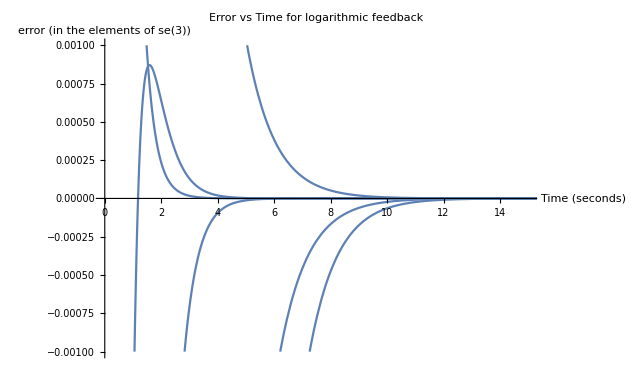

```mathematica
Plot[(z[t]/.logerror), {t, 0, 50}, PlotRange->{{0, 15}, {-0.001, 0.001}}, AxesLabel->{"Time (seconds) ", "error (in the elements of se(3))"} , PlotLabel->"Error vs Time for logarithmic feedback"]
```

```mathematica
(*Finding the values of the actual elements*)
```

```mathematica
R62dual[z_]:=Module[{},
Return[{z[[1;;3]],z[[4;;6]]}];
]
```

```mathematica
R62dual[z[t]/.logerror/.t->0.1]
```

{{-0.452889,0.139961,-1.28409},{-0.0862895,-0.194512,0.0553782}}

```mathematica
(*This solves the regulation problem using se3*)
```

```mathematica
(*Now to see the differences in the path taken by both these methods we need to plot the end-effector location and orientation*)
```

```mathematica
(*So we need to start making a visualisation module*)
```

```mathematica
(*/.Point[a___]:>{Thick,Line[a]}*)
```

```mathematica
logdq[N[fkq/.sampleangles]/.params]
logdq[N[fkq/.sampleangles2]/.params]
```

{{-2.63132,0.470235,-0.953744},{0.0651801,0.153568,0.0241239}}

{{-0.42751,0.473106,-1.28564},{-0.0625,-0.0290251,-0.11745}}

```mathematica
fkm1 = fkq/.params/.Table[Inner[Rule, θsym, ((z[t]/.motionsim)/.t->tval)[[1;;6]], List],{tval, 0, 15, 0.05}];
```

```mathematica
config2 = Table[Flatten[logdq[fkm1[[i]]]],{i, 301}];
```

```mathematica
config2//Dimensions
```

{301,6}

```mathematica
ListPointPlot3D[config2[[;;,1;;3]]]
```

-Graphics3D-

```mathematica
config2angles = Table[logdq[fkm1[[i]]][[1]],{i, 301}];
```

```mathematica
ListPointPlot3D[config2angles]
```

-Graphics3D-

```mathematica
(*To visualise the complete motion we need a marker axes which moves with the end-effector*)
```

```mathematica
(*Verifying the properties of logarithm for dual quaternions*)
```

```mathematica
tempei = dqmult[cdualq[qd], qi]
```

{{0.0580127,{-0.33031,0.102079,-0.936541}},{0.0527857,{0.195699,-0.147976,-0.0818806}}}

```mathematica
Chop[dqmult[qd, tempei]-qi]
```

{{0,{0,0,0}},{0,{0,0,0}}}

```mathematica
logdq[tempei]
```

{{-0.50052,0.154681,-1.41914},{-0.118155,-0.224299,0.0735869}}

```mathematica
logdq[cdualq[qd]]+logdq[qi]
```

{{-2.20381,-0.002871,0.331893},{0.0544508,0.0572737,0.119808}}

```mathematica
(*Not the same!*)
```

```mathematica
logdq[dqmult[qd, tempei]]
```

{{-2.63132,0.470235,-0.953744},{0.0651801,0.153568,0.0241239}}

```mathematica
logdq[qi]
```

{{-2.63132,0.470235,-0.953744},{0.0651801,0.153568,0.0241239}}

```mathematica
(*Hence the normal logarithmic identities do not work for dual quaternions as the multiplication here has different rules*)
```

```mathematica
explogdq[logdq_]:=Module[{tempθ, tempk},
tempθ = Norm[logdq[[1]]];
tempk = logdq[[1]]/tempθ;
Return[unitdq[2*logdq[[2]], 2*tempθ, tempk]];
];
```

```mathematica
Chop[dqmult[qd, explogdq[logdq[ei]]]-qi]
```

{{0,{0,0,0}},{0,{0,0,0}}}

```mathematica
logdq[dqmult[qd,explogdq[R62dual[z[t]/.logerror/.t->0]]]]
```

{{-2.63132,0.470235,-0.953744},{0.0651801,0.153568,0.0241239}}

```mathematica
config = Table[Flatten[logdq[dqmult[qd,explogdq[R62dual[z[t]/.logerror/.t->tval]]]]],{tval, 0, 15, 0.05}];
```

```mathematica
pl1 = ListPointPlot3D[config[[;;,1;;3]], PlotStyle->{Red}, PlotRange->{{-1,-0.4},{0,1},{-3, 3}}];
pl2 = ListPointPlot3D[config2[[;;,1;;3]]];
Show[pl1,pl2]
```

-Graphics3D-

```mathematica
(*Though interpreting these plots doesnt make sense, we can see that in the second case i.e. in config2 case, the change in the angles and the axis is very small compared to the other case*)
```

```mathematica
logdq[qi][[2]]
logdq[qd][[2]]
```

{0.0651801,0.153568,0.0241239}

{-0.0625,-0.0290251,-0.11745}

```mathematica
Show[ListPointPlot3D[2*config2[[;;,4;;6]], PlotStyle->{Green}], ListPointPlot3D[2*config[[;;,4;;6]], PlotStyle->{Red}], PlotRange->{{-1, 1}, {-1, 1}, {-0.3, 0.2}}]
```

-Graphics3D-

```mathematica
config[[1]]
config2[[1]]
config[[-1]]
config2[[-1]]
```

{-2.63132,0.470235,-0.953744,0.0651801,0.153568,0.0241239}

{-2.63132,0.470235,-0.953744,0.0651801,0.153568,0.0241239}

{-0.42751,0.473106,-1.28564,-0.0625,-0.0290251,-0.11745}

{-0.427538,0.473113,-1.28563,-0.0626612,-0.0290418,-0.117443}